```mathematica
Get["D:\\pre25000.m"]
```

{24,24,24,96,24,96,120,24,24,24,120,24,24,96,96,24,24,72,96,96,288,24,24,24,96,120,24,24,24,96,120,24,24,24,96,72,288,72,120,216,144,120,120,120,120,48,24,24,96,24,24,24,24,24,24,96,96,24,24,24,24,384,96,96,96,96,96,24,24,24,24,504,24,24,24,120,24,96,96,288,24,96,24,24,24,24,24,72,120,120,216,24818,216,216,216,216,216,216,1080,456,216,192,144,384,312,72,288,336,144,144,216,72,72,72,72,72,72,72,72,72,72,72,72,240,312,264,480,120,288,72,480,120,120,120,120,120,120,120,120,120,120,120,120,120,312,600,600,600,264,1152,288,480,480,480,480,480,480,480,480,480,480,480,480,480,360,168,528,312,312,312,168,144,144,144,144,144,144,144,144,144,144,144,144}
 |  |  |  |

```mathematica
Length[pre]
```

500000

```mathematica
Take[pre,100]/24
```

{1,1,1,4,1,4,5,1,1,1,5,1,1,4,4,1,1,3,4,4,12,1,1,1,4,5,1,1,1,4,5,1,1,1,4,3,12,3,5,9,6,5,5,5,5,2,1,1,4,1,1,1,1,1,1,4,4,1,1,1,1,16,4,4,4,4,4,1,1,1,1,21,1,1,1,5,1,4,4,12,1,4,1,1,1,1,1,3,5,5,9,1,4,3,4,4,4,16,3,5}

```mathematica
jake=ReadList["d:\\colofour.txt",Number,100]
```

{24,24,24,96,24,96,120,24,24,24,120,24,24,96,96,24,24,72,96,96,288,24,24,24,96,120,24,24,24,96,120,24,24,24,96,72,288,72,120,216,144,120,120,120,120,48,24,24,96,24,24,24,24,24,24,96,96,24,24,24,24,384,96,96,96,96,96,24,24,24,24,504,24,24,24,120,24,96,96,288,24,96,24,24,24,24,24,72,120,120,216,24,96,0,96,96,96,384,72,120}

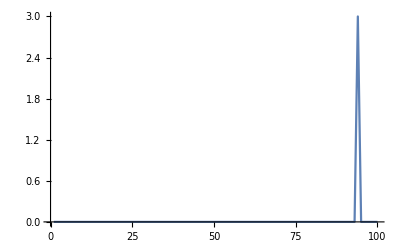

```mathematica
ListLinePlot[Table[{i,(pre[[i]]-jake[[i]])/24},{i,1,100}]]
```

```mathematica
ChromaticPolynomial[ReadGrof[93],4]
```

96

```mathematica
jake[[93]]
```

0